## Define noise

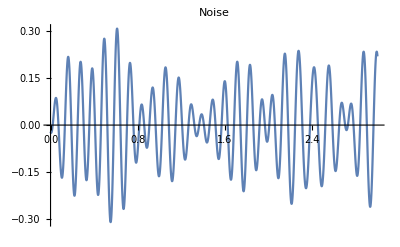

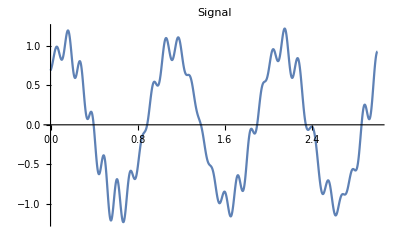

```mathematica
SetDirectory@NotebookDirectory[];
tf=3;
Δt=0.01;

SeedRandom[1];
sineSum=Plus@@Table[RandomReal[{-0.1,0.1}]Sin[40(1+ j/20)  t+2π RandomReal[]],{j,1,10,1}];
noise[t_]:=Evaluate[sineSum];
Plot[noise[t],{t,0,3},PlotLabel->"Noise"]

system[t_]:=Sin[2π f0 t+π/4]/.f0->1;
signal[t_]:=system[t]+noise[t];
Plot[signal[t],{t,0,3},PlotLabel->"Signal"]
```

## Signal and filtering

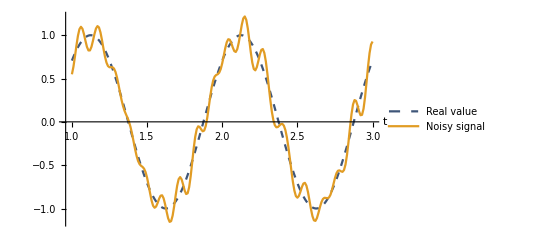

```mathematica
tSamples=Range[1,tf,Δt];
signalSamples=signal/@tSamples;
systemSamples=system/@tSamples;

noisyPlot=ListLinePlot[
{
Transpose@{tSamples,systemSamples},
Transpose@{tSamples,signalSamples}
},
PlotStyle->{
{Thick,Dashed,Darker@RGBColor[0.368417, 0.506779, 0.709798]},
{RGBColor[0.880722, 0.611041, 0.142051]}},
AxesLabel->{"t",None},LabelStyle->Directive[FontSize->15,FontColor->Black],
PlotLegends->Placed[{"Real value","Noisy signal"},Above],Ticks->{None,None},Axes->{Automatic,None},AxesStyle->Black]

Export["img_NoisySignal.png",noisyPlot];
```

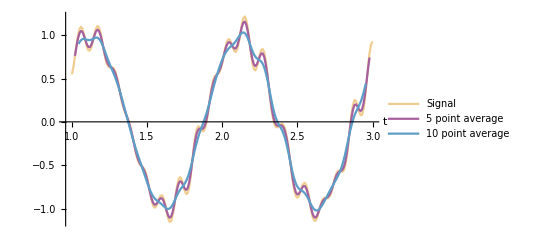

```mathematica
nMany=10;
kernelMany=ConstantArray[1./nMany,nMany];
filteredMany=ListConvolve[kernelMany,signalSamples];
tSamplesMany=ListConvolve[kernelMany,tSamples];

nFew=5;
kernelFew=ConstantArray[1./nFew,nFew];
filteredFew=ListConvolve[kernelFew,signalSamples];
tSamplesFew=ListConvolve[kernelFew,tSamples];

filteredPlot=ListLinePlot[
{
Transpose@{tSamples,signalSamples},
Transpose@{tSamplesFew,filteredFew},
Transpose@{tSamplesMany,filteredMany}(*,
Transpose@{tSamples,systemSamples}*)
},
PlotStyle->{
{RGBColor[0.880722, 0.611041, 0.142051],Opacity[0.5]},
{RGBColor[0.647624, 0.37816, 0.614037]},
{RGBColor[0.363898, 0.618501, 0.782349],Thick}(*,
{Darker@RGBColor[0.363898, 0.618501, 0.782349],Thick,Dashed,Opacity[0.5]}*)},
AxesLabel->{"t",None},LabelStyle->Directive[FontSize->15,FontColor->Black],
PlotLegends->Placed[{"Signal",ToString[nFew]<>" point average",ToString[nMany]<>" point average"},Above],
Ticks->{None,None},Axes->{Automatic,None},AxesStyle->Black]
Export["img_FilteredSignal.png",filteredPlot];
```

## Kernel and Fourier transform

```mathematica
hFourier=Sinc[f];
hTime=FourierTransform[Sinc[f],f,t];

xRange=All;
yRange={-0.25,1.3};
ar=1.2;

sincPlot=Plot[Callout[Sinc[f],Style["sinc(f)",FontColor->RGBColor[0.368417, 0.506779, 0.709798]],{Scaled[0.125],Above}],{f,0,20},PlotRange->{xRange,yRange},PlotRangePadding->None,AxesLabel->{"f",None},Ticks->{None,None},LabelStyle->Directive[FontSize->25,FontColor->Black],Exclusions->None,AxesStyle->Black,ImageSize->Medium,AspectRatio->ar,PlotStyle->Thick];
hkPlot=Plot[Callout[hTime,Style["h(k)",FontColor->RGBColor[0.880722, 0.611041, 0.142051]],{2,1.1},{1,1.1}],{t,0,5},PlotRange->{xRange,yRange},PlotRangePadding->None,AxesLabel->{"k",None},Ticks->{None,None},LabelStyle->Directive[FontSize->25,FontColor->Black],Exclusions->None,AxesStyle->Black,PlotStyle->{Thick,RGBColor[0.880722, 0.611041, 0.142051]},ImageSize->Medium,AspectRatio->ar];
kernelPlots=Row[{hkPlot," ",sincPlot}]
Export["img_hkFourier.png",kernelPlots];
```

-Graphics- -Graphics-